```mathematica
Clear["Global`*"]
BasisFunc[n_]:=Function[{x},Sqrt[(2n+1)/2]LegendreP[n,x]]
BasisMax=10;

qFunc[x_]=PDF[NormalDistribution[0.1,0.2],x];

(*Plot[Evaluate[Table[BasisFunc[n][x],{n,0,BasisMax}]],{x,-1,1}]*)
```

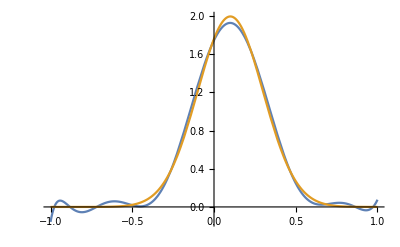

{-4.12546,16.1873,-4.09697,25.3596,-20.9989,15.8573,0.869546,29.1889,-16.8327,0.,0.}

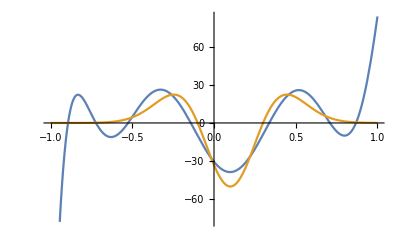

```mathematica
q=Table[NIntegrate[qFunc[x]BasisFunc[n][x],{x,-1,1}],{n,0,BasisMax}];
Plot[{q.Table[BasisFunc[n][x],{n,0,BasisMax}],qFunc[x]},{x,-1,1},PlotRange->All]


(LegDerivative={ConstantArray[0,Max[BasisMax]+1]}~Join~Table[Normal[SparseArray[Band[l,1,-2]->Array[(2(l-2#)-1)&,Quotient [l,2]+1,0],{Max[BasisMax]+1}]],{l,1,Max[BasisMax]}])//MatrixForm;
(LegDerivative=Transpose[MapIndexed[#1Sqrt[(2#2[[1]]-1)/(2#2[[2]]-1)]&,LegDerivative,{2}]])//MatrixForm;

MatrixPower[LegDerivative,2].q
Plot[{%.Table[BasisFunc[n][x],{n,0,BasisMax}],Evaluate[D[qFunc[x],{x,2}]]},{x,-1,1}]
```

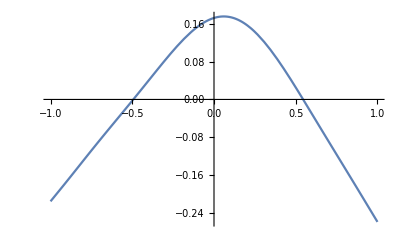

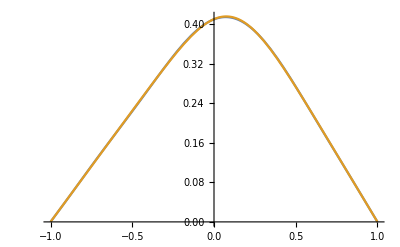

```mathematica
T=-Inverse[MatrixPower[LegDerivative,2][[;;-3,3;;]]].(q[[;;-3]]);
Plot[{T.Table[BasisFunc[n][x],{n,2,BasisMax}]},{x,-1,1},PlotRange->All]

T={-T.(Table[BasisFunc[n][1],{n,2,BasisMax}]-Table[BasisFunc[n][-1],{n,2,BasisMax}])/2/BasisFunc[1][1]}~Join~T;
T={-T.Table[BasisFunc[n][1],{n,1,BasisMax}]/BasisFunc[0][1]}~Join~T;

sol=y/.NDSolve[{y''[x]==-qFunc[x],y[-1]==0,y[1]==0},y,x][[1]];
Plot[{T.Table[BasisFunc[n][x],{n,0,BasisMax}],sol[x]},{x,-1,1},PlotRange->All]
```

Домашнее задание
1) Найти решение семинарской задачи с граничными условиями y[-1]=a, y’[-1]=b.
2) Решить уравнение Пуассона на отрезке от -1 до 1 методом Релея-Ритца:

Выразить функционал через вектор столбец коэффициентов искомой функции.
Создать область в которой будут меняться искомые коэффициенты. Она будет размерности BasisMax+1. Возможно пригодится оператор Cuboid.
Найти минимум функционала в созданной области. Возможно будет полезен оператор NMinimize.
Построить функцию по найденным коэффициентам.

Какое граничное условие “зашито” в метод Рэлея-Ритца? Уметь доказать это на бумаге.

3) Изменить функционал так, чтобы находилась функция с граничными условиями Неймана y’[-1]=a, y’[1]=b
4) Найти решение, удовлетворяющее граничным условиям Дирихле y[-1]=a, y[1]=b. Возможно для этого придется повнимательней просмотреть хелп оператора NMinimize